```mathematica
Clear[repv]
```

```mathematica
repv={ps->15,qs->2,lambda->1,Q->0.07,r->-0.01,x->1.*^-13,y->1.*^-14};
```

```mathematica
oc={omc->1-omphi-omb-omr};
rept={x->x[t], y->y[t], omb->omb[t], omr->omr[t],X1->X1[t],X2->X2[t],Y1->Y1[t],Y2->Y2[t]};

Clear[omphi,wphi, g1,g1dotOH,wm]
```

```mathematica
Clear[ps,qs,lambda,Q,r]
```

```mathematica
omphi=FullSimplify[((ps*x^2-r*y^2)*(qs*x^2+y^2)-2*r*y^2)/(ps*x^2-3*r*y^2)];
wphi=FullSimplify[(qs*x^2-y^2)/omphi];
qs=2;
Q=0.07;
lambda=1;
r=-0.01;
ps=15;
wm=0;
Clear[ps,qs,lambda,Q,r]
g1=ps-r*y^2/x^2;
```

```mathematica
OMPHI=omphi/.rept;
```

```mathematica
Clear[ephi,omphidotOH,eps]
```

```mathematica
Clear[qs,Q,lambda,r,s,ps]
```

```mathematica
g1dotOH=FullSimplify[2*r*(y^2/x^2)*(lambda*Sqrt[6]/2*x+ephi)];
eps=FullSimplify[(-3/2*omphi(1+wphi)-3/2*omc*(1+wm)-3/2*omb*(1+wm)-2*omr)];
```

```mathematica
omphidotOH=Simplify[((2*r*y^2*(lambda*Sqrt[6]/2*x+eps)+2*ps*x^2*(ephi-eps))*(qs*x^2+y^2)+(ps*x^2-r*y^2)*(2*qs*x^2*ephi-lambda*x*y^2*Sqrt[6]-2*eps*(qs*x^2+y^2))+4*r*y^2*(lambda*Sqrt[6]/2*x+eps))*((ps*x^2-3*r*y^2)^-1)-((ps*x^2-r*y^2)*(qs*x^2+y^2)-2*r*y^2)*(2*x^2*ps*(ephi-eps)+6*r*y^2*(lambda*Sqrt[6]/2*x+eps))/(ps*x^2-3*r*y^2)^2];
```

```mathematica
Clear[Ephi, EPHI]
```

```mathematica
Ephi=Simplify[Solve[omphidotOH+2*omphi*eps+3*omphi(1+wphi)==(-Sqrt[6]*Q*x-g1dotOH/g1)*omc,ephi]];
```

```mathematica
EPHI=ephi/.Ephi[[1]];
```

```mathematica
Clear[eq1,eq2,eq3,eq4]
```

```mathematica
eq1=Simplify[x*(EPHI-eps)]/.oc;
```

```mathematica
eq2=Simplify[-y*(x*Sqrt[6]/2*lambda+eps)]/.oc;
```

```mathematica
eq3=Simplify[-omb (2*eps+3(1+wm))]/. oc;
```

```mathematica
eq4=Simplify[-omr (2*eps+4)]/. oc;
```

```mathematica
Clear[EQ1,EQ2,EQ3,EQ4]
```

```mathematica
EQ1=eq1/.rept;
```

```mathematica
EQ2=eq2/.rept;
```

```mathematica
EQ3=eq3/.rept;
```

```mathematica
EQ4=eq4/.rept;
```

```mathematica
qs=2;
Q=0.07;
lambda=1;
r=-0.01;
ps=15;
```

```mathematica
Clear[EQNS,Sol]
```

```mathematica
EQNS={x'[t]==EQ1,y'[t]==EQ2,omb'[t]==EQ3,omr'[t]==EQ4,x[-18.234]==1.*^-13,y[-18.234]==1.*^-14,omb[-18.234]==5.7999999999999995*^-6,omr[-18.234]==0.999962};
```

```mathematica
Sol=NDSolve[EQNS,{x[t],y[t],omb[t],omr[t]},{t,-18.234,5}];
```

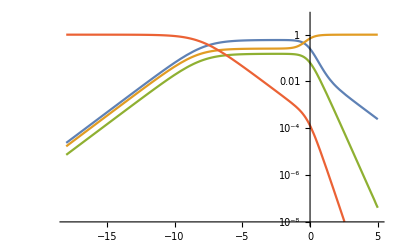

```mathematica
LogPlot[{(1-OMPHI-omb[t]-omr[t])/.Sol,OMPHI/.Sol,omb[t]/.Sol,omr[t]/.Sol},{t,5,-18},PlotRange->{10^-8,6}]
```

```mathematica
Clear[weffe]
```

```mathematica
weffe=-1-2/3*eps;
```

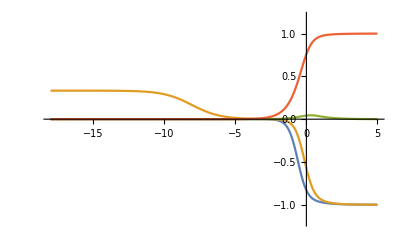

```mathematica
Plot[{wphi/.x->x[t]/.y->y[t]/.Sol,weffe/.oc/.omr->omr[t]/.omb->omb[t]/.x->x[t]/.y->y[t]/.Sol,x[t]/.Sol,y[t]/.Sol},{t,5,-18},PlotRange->{-1.2,1.2}]
```

```mathematica
Clear[ps,qs,lambda,Q,r]
```

```mathematica
Clear[acceleratedpoint2,phiMDEpoint2,other2,otherpoints2]
```

```mathematica
omb=0;omr=0;
```

```mathematica
acceleratedpoint2=Solve[{eq1==0, eq2==0},{x,y}]
```

$Aborted

```mathematica
acceleratedpoint2
```

{{x→(√(3/2))/(lambda+Q),y→-(√(2 lambda Q+2 Q^2+3 qs))/(√2 (lambda+Q))},{x→(√(3/2))/(lambda+Q),y→(√(2 lambda Q+2 Q^2+3 qs))/(√2 (lambda+Q))},{x→lambda/(√6 qs),y→-(√(-lambda^2+6 qs))/(√6 √qs)},{x→lambda/(√6 qs),y→(√(-lambda^2+6 qs))/(√6 √qs)},{x→-(√(2/3) Q)/qs,y→0},{x→-1/(√qs),y→0},{x→1/(√qs),y→0},{x→(-√6 lambda r-√6 √(2 ps r+lambda^2 r^2-6 qs r^2))/(2 (ps-3 qs r)),y→-(√(3+(9 ps qs r)/(ps-3 qs r)^2+(9 lambda^2 qs r^2)/(ps-3 qs r)^2-(27 qs^2 r^2)/(ps-3 qs r)^2+(3 lambda^2 r)/(ps-3 qs r)+(9 lambda qs r √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)^2+(3 lambda √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)))/(√3)},{x→(-√6 lambda r-√6 √(2 ps r+lambda^2 r^2-6 qs r^2))/(2 (ps-3 qs r)),y→(√(3+(9 ps qs r)/(ps-3 qs r)^2+(9 lambda^2 qs r^2)/(ps-3 qs r)^2-(27 qs^2 r^2)/(ps-3 qs r)^2+(3 lambda^2 r)/(ps-3 qs r)+(9 lambda qs r √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)^2+(3 lambda √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)))/(√3)},{x→(-√6 lambda r+√6 √(2 ps r+lambda^2 r^2-6 qs r^2))/(2 (ps-3 qs r)),y→-(√(3+(9 ps qs r)/(ps-3 qs r)^2+(9 lambda^2 qs r^2)/(ps-3 qs r)^2-(27 qs^2 r^2)/(ps-3 qs r)^2+(3 lambda^2 r)/(ps-3 qs r)-(9 lambda qs r √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)^2-(3 lambda √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)))/(√3)},{x→(-√6 lambda r+√6 √(2 ps r+lambda^2 r^2-6 qs r^2))/(2 (ps-3 qs r)),y→(√(3+(9 ps qs r)/(ps-3 qs r)^2+(9 lambda^2 qs r^2)/(ps-3 qs r)^2-(27 qs^2 r^2)/(ps-3 qs r)^2+(3 lambda^2 r)/(ps-3 qs r)-(9 lambda qs r √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)^2-(3 lambda √(2 ps r+lambda^2 r^2-6 qs r^2))/(ps-3 qs r)))/(√3)}}

```mathematica
omphi/.acceleratedpoint2/.repv
```

{5.29433,5.29433,1.,1.,0.00163333,1,1,1.34589×10^13-5.16085×10^13 ⅈ,1.34589×10^13-5.16085×10^13 ⅈ,1.34589×10^13+5.16085×10^13 ⅈ,1.34589×10^13+5.16085×10^13 ⅈ}

```mathematica
wphi/.acceleratedpoint2/.repv
```

{-0.0123567,-0.0123567,-0.833333,-0.833333,1,1,1,-4.06723×10^-15-1.83031×10^-14 ⅈ,-4.06723×10^-15-1.83031×10^-14 ⅈ,-4.06723×10^-15+1.83031×10^-14 ⅈ,-4.06723×10^-15+1.83031×10^-14 ⅈ}

```mathematica
Clear[omb,omr]
```

```mathematica
omb=0;omr=0;y=0;
```

```mathematica
phiMDEpoint2=Solve[eq1==0,x];
```

```mathematica
omphi/.phiMDEpoint2;
```

```mathematica
wphi/.phiMDEpoint2;
```

```mathematica
Clear[omb,omr,y]
```

```mathematica
omb=0;y=0;
other2=Solve[{eq1==0,eq4==0},{x,omr}]
```

```mathematica
omphi/.other2;
wphi/.other2;
```

```mathematica
Clear[omb,y]
```

{{x→0,omr→1},{x→-1/(√6 Q),omr→(2 Q^2-qs)/(2 Q^2)},{x→-(√(2/3) Q)/qs,omr→0},{x→-1/(√qs),omr→0},{x→1/(√qs),omr→0}}

```mathematica
omb=0;
otherpoints2=Solve[{eq1==0,eq2==0,eq4==0},{x,y,omr}]
```

$Aborted

```mathematica
omphi/.otherpoints2;
wphi/.otherpoints2;
```

```mathematica
Clear[omb]
```